```mathematica
g=9.8
a=0.2
```

9.8

0.2

```mathematica
eqn=v'[t]==g-a*v[t]
```

v'[t]==9.8-0.2 v[t]

```mathematica
ics=v[0]==0
```

v[0]==0

```mathematica
DSolve[{eqn,ics},v, t]
```

{{v→Function[{t},49. ⅇ^(-0.2 t) (-1.+1. ⅇ^(0.2 t))]}}

```mathematica
f[t_]=v[t]/.%[[1]]
```

49. ⅇ^(-0.2 t) (-1.+1. ⅇ^(0.2 t))

```mathematica
f[40]
```

48.9836

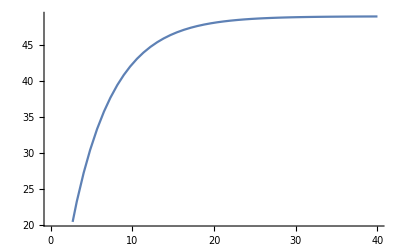

```mathematica
Plot[f[t], {t,0,40}]
```

```mathematica
DSolve[{v'[t]==g-a v[t], v[0]==0}, v, t]
```

{{v→Function[{t},(ⅇ^(-a t) (-1+ⅇ^(a t)) g)/a]}}